## Notebook Setups

```mathematica
$HistoryLength=0;
```

#### Formatting

```mathematica
LMR="Latin Modern Roman";
Av="Avenir";
Ar="Arial";
TNR="Times New Roman";
BOS="Bookman Old Style";
fontfam=LMR;
nmbrsize=14;
labelsize=12;
episize=12;
framethick=0.003;
thick=0.005;
fs=Directive[{Black,FontFamily->fontfam,FontSize->nmbrsize,Thickness[framethick]}];
```

#### Import

```mathematica
importSetup[paramNames_,paramTypes_,dir_,setupFilename_]:=AssociationThread[paramNames->Import[dir<>setupFilename,"Binary","DataFormat"->paramTypes][[1]]];
```

```mathematica
importReal64MultiList[dir_,template_]:=Module[{filenameTemplate,depth,dimensions,imported},
filenameTemplate=StringTemplate[template];
depth=StringCount[template,"``"];
dimensions=(Length[FileNames[#,dir,1]]&)@*(TemplateApply[filenameTemplate,Table[If[i==#,"*",0],{i,depth}]]&)/@Range[depth];
imported=Array[Import[dir<>filenameTemplate[##],"Real64"]&,dimensions,ConstantArray[0,depth]];
{dimensions,imported}
];
```

#### Intermediaries

```mathematica
computekSpectrumPoints[setup_]:=Module[{n=setup[["N"]],L=setup[["L"]]},(2π)/L √Range[0,3(n/2)^2]];
```

```mathematica
computeBins[setup_]:=Module[{n=setup[["N"]],L=setup[["L"]]},BinLists[Range[0,3(setup["N"]/2)^2],{Table[k^2,{k,0,setup["N"]/2}]}]];
computeBinnedkSpectrumPoints[setup_]:=Module[{n=setup[["N"]],L=setup[["L"]]},(2π)/setup["L"] Range[0,setup["N"]/2-1]];
```

```mathematica
computeMultiplicityList[n_?NumberQ]:=Sort@Tally@Flatten@Array[(#1^2+#2^2+#3^2&),{n,n,n},{-n/2+1,-n/2+1,-n/2+1}];
computeMultiplicityList[setup_]:=computeMultiplicityList[setup[["N"]]];
```

```mathematica
ClearAll[intermediaries];
intermediaries=CreateDataStructure["HashTable"];
```

```mathematica
computeIntermediaries[setup_]:=Module[{kSpectrumPoints,multiplicityList,indicesOfNonZeroMultiplicity,nonZeroMultiplicity,bins,binnedkSpectrumPoints,intermediariesForSetup},
kSpectrumPoints=computekSpectrumPoints[setup];
bins=computeBins[setup];
binnedkSpectrumPoints=computeBinnedkSpectrumPoints[setup];
multiplicityList=computeMultiplicityList[setup];
indicesOfNonZeroMultiplicity=multiplicityListᵀ[[1]];
nonZeroMultiplicity=multiplicityListᵀ[[2]];
intermediariesForSetup["kSpectrumPoints"]=kSpectrumPoints;
intermediariesForSetup["bins"]=bins;
intermediariesForSetup["binnedkSpectrumPoints"]=binnedkSpectrumPoints;
intermediariesForSetup["multiplicityList"]=multiplicityList;
intermediariesForSetup["indicesOfNonZeroMultiplicity"]=indicesOfNonZeroMultiplicity;
intermediariesForSetup["nonZeroMultiplicity"]=nonZeroMultiplicity;
intermediaries["Insert",Hash[setup]->intermediariesForSetup];
];
```

```mathematica
getIntermediary[setup_,name_]:=If[MissingQ[intermediaries["Lookup",Hash[setup]]],
computeIntermediaries[setup];intermediaries["Lookup",Hash[setup]][name],
intermediaries["Lookup",Hash[setup]][name]];
```

#### Spectrums

```mathematica
ClearAll[computeSmoothedPowerSpectrum,computeBinnedSpectrum];
```

```mathematica
computeBinnedSpectrum[setup_,spectrum_]:=Module[{
kSpectrumPoints=getIntermediary[setup,"kSpectrumPoints"],
bins=getIntermediary[setup,"bins"],
binnedkSpectrumPoints=getIntermediary[setup,"binnedkSpectrumPoints"]},
{binnedkSpectrumPoints,Total[spectrum[[#+1]]]&/@bins}ᵀ
];
```

## Plotting animation

```mathematica
dir=NotebookDirectory[]<>"output/FS_Without_Gravity/";
(*dir=NotebookDirectory[]<>"../../Data/ThreeWayCompare_Animation_2/";*)
paramNames=Import[dir<>"paramNames.txt","List"];
paramTypes=Import[dir<>"paramTypes.txt","List"];
setup=importSetup[paramNames,paramTypes,dir,"param.dat"]
```

<|N→384,L→307.2,m→1.,lambda→0.,f_a→10.,k_ast→1.,k_Psi→0.3,varphi_std_dev→1.,Psi_std_dev→0.15,a1→1.,H1→0.05,t1→10.,t_start→10.,t_end→10.1,t_interval→49.99,delta_t→0.5,M→128|>

```mathematica
{{numSnapshots},ρList}=importReal64MultiList[dir,"rho_slice_``.dat"];
```

```mathematica
{{numSnapshots},ρAverageList}=importReal64MultiList[dir,"rho_axis_average_``.dat"];
```

```mathematica
ClearAll[ρMeanList,ρGridList,δGridList,δRange,ρAverageMeanList,ρAverageGridList,δAverageGridList,δAverageRange]
```

```mathematica
ρMeanList=Mean/@ρList;
ρGridList=Partition[#,setup[["N"]]]&/@ρList;
δGridList=MapThread[(#1/#2-1.0&),{ρGridList,ρMeanList}];
(*δRange=δGridList//Flatten//MinMax;*)
```

```mathematica
ρAverageMeanList=Mean/@ρAverageList;
ρAverageGridList=Partition[#,setup[["N"]]]&/@ρAverageList;
δAverageGridList=MapThread[(#1/#2-1.0&),{ρAverageGridList,ρAverageMeanList}];
(*δAverageRange=δAverageGridList//Flatten//MinMax;*)
```

```mathematica
tList=Import[dir<>"t_list.dat","Real64"];
mtLegendList=Table[StringTemplate["mt=`t`"][<|"t"->setup["m"] tList[[i]]|>],{i,Length@tList}];
```

```mathematica
a1=setup["a1"];H1=setup["H1"];t1=setup["t1"];
aList=a1(1+2H1(tList[[1;;numSnapshots]]-t1))^(1/2);
HList=H1(aList/a1)^-2;
```

#### Load WKB solution

```mathematica
{{numSnapshots},WKBρAverageList}=importReal64MultiList[dir,"wkb_rho_axis_average_``.dat"];
```

```mathematica
WKBρAverageMeanList=Mean/@WKBρAverageList;
WKBρAverageGridList=Partition[#,setup[["N"]]]&/@WKBρAverageList;
WKBδAverageGridList=MapThread[(#1/#2-1.0&),{WKBρAverageGridList,WKBρAverageMeanList}];
(*δAverageRange=δAverageGridList//Flatten//MinMax;*)
```

```mathematica
CombinedδAverageGridList=δAverageGridList~Join~WKBδAverageGridList;
```

```mathematica
WKBtList=Import[dir<>"wkb_t_list.dat","Real64"]*setup["t_end"];
WKBmtLegendList=Table[StringTemplate["mt=`t`"][<|"t"->setup["m"] WKBtList[[i]]|>],{i,Length@WKBtList}];
```

```mathematica
CombinedtList=tList~Join~WKBtList;
CombinedmtLegendList=mtLegendList~Join~WKBmtLegendList;
```

```mathematica
WKBaList=a1(1+2H1(WKBtList-t1))^(1/2);
WKBHList=H1(WKBaList/a1)^-2;
```

```mathematica
CombinedaList=aList~Join~WKBaList;
CombinedHList=HList~Join~WKBHList;
```

```mathematica
(*CombinedHList//ListLogPlot*)
```

#### Setup the color scheme

```mathematica
dcf="DefaultColorFunction"/. Themes`DefaultStyles[MatrixPlot][[All,2]];
```

```mathematica
legendRangeForδAverage={-1,1.5};
legendRangeForδ={-1,15};
```

```mathematica
dcfRangeForδAverage={-0.5,1};
dcfRangeForδ={-1,10};
dcfForδAverage=dcf@*(If[#>0,0.5(1+#/dcfRangeForδAverage[[2]]),0.5(1+#/(-dcfRangeForδAverage[[1]]))]&);
dcfForδ=dcf@*(If[#>0,0.5(1+#/dcfRangeForδ[[2]]),0.5(1+#/(-dcfRangeForδ[[1]]))]&);
```

```mathematica
(*MatrixPlot[δGridList[[1]],PlotLegends->BarLegend[{Automatic,legendRangeForδ},LegendLabel->"δ"],ColorFunctionScaling->False,ColorFunction->dcfForδ]*)
```

```mathematica
(*MatrixPlot[δAverageGridList[[1]],PlotLegends->BarLegend[{Automatic,legendRangeForδAverage},LegendLabel->"δ"],ColorFunctionScaling->False,ColorFunction->dcfForδAverage]*)
```

#### Filtering

```mathematica
filterWindow[setup_,image_,kMin_,kMax_]:=Module[{fft,fftFiltered,n=setup["N"]},
fft=Fourier[image,FourierParameters->{1,-1}];
fftFiltered=Table[
aShifted=If[a-1<=n/2,a-1,n-(a-1)];
bShifted=If[b-1<=n/2,b-1,n-(b-1)];
If[kMin^2/((2π)/setup["L"])^2<=aShifted^2+bShifted^2<=kMax^2/((2π)/setup["L"])^2,fft[[a,b]],0],{a,1,n},{b,1,n}];
Re[InverseFourier[fftFiltered,FourierParameters->{1,-1}]]
];
```

```mathematica
(*Array[(#1^2+#2^2+#3^2&),{n,n,n},{-n/2+1,-n/2+1,-n/2+1}];*)
```

```mathematica
fft=Fourier[δGridList[[-1]],FourierParameters->{1,-1}];
```

```mathematica
n=setup["N"];
```

```mathematica
(*fft//Abs//MatrixPlot*)
```

```mathematica
kMin=0.07;
kMax=0.3;
fftFiltered=Table[
aShifted=If[a-1<=n/2,a-1,n-(a-1)];
bShifted=If[b-1<=n/2,b-1,n-(b-1)];
If[kMin^2/((2π)/setup["L"])^2<=aShifted^2+bShifted^2<=kMax^2/((2π)/setup["L"])^2,fft[[a,b]],0],{a,1,n},{b,1,n}];
```

```mathematica
(*fftFiltered//Abs//MatrixPlot*)
```

```mathematica
filtered=Re[InverseFourier[fftFiltered,FourierParameters->{1,-1}]];
```

```mathematica
MatrixPlot[filtered*10,
PlotLegends->BarLegend[{Automatic,legendRangeForδ},LabelStyle->{FontFamily->fontfam,FontSize->12}],
ColorFunctionScaling->False,ColorFunction->dcfForδ,
FrameStyle->Directive[{Black,FontFamily->fontfam,FontSize->12,Thickness[framethick]}],
FrameTicks->{Map[{#,setup["L"]/setup["N"]#}&,Table[100i,{i,0,Floor[setup["N"]/100]}],-1]},
PlotLabel->Style["δ (slice)",Black,{FontFamily->fontfam,FontSize->18}],
ImageSize->Medium]
```

-Graphics-

```mathematica
(*filterWindow[setup,δAverageGridList[[10]],0.07,0.2]//MatrixPlot*)
```

```mathematica
δGridFilteredList=filterWindow[setup,#,0.06,0.08]&/@δGridList[[{1,40,-1}]];
```

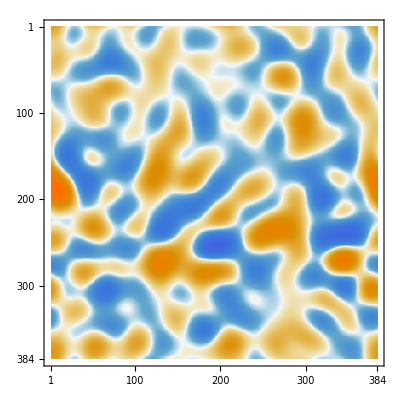

```mathematica
δGridFilteredList[[-1]]//MatrixPlot
```

#### Animation for δ

```mathematica
δGridList//Dimensions
```

{721,384,384}

```mathematica
AbsoluteTiming[δAnimation=Table[
Rasterize[#,RasterSize->800]&@MatrixPlot[20δGridFilteredList[[i]],
(*PlotLegends->BarLegend[{Automatic,legendRangeForδ},LegendLabel->"δ"],*)
PlotLegends->BarLegend[{Automatic,legendRangeForδ},LabelStyle->{FontFamily->fontfam,FontSize->12}],
ColorFunctionScaling->False,ColorFunction->dcfForδ,
FrameStyle->Directive[{Black,FontFamily->fontfam,FontSize->12,Thickness[framethick]}],
FrameTicks->{Map[{#,setup["L"]/setup["N"]#}&,Table[100i,{i,0,Floor[setup["N"]/100]}],-1]},
PlotLabel->Style["δ (slice)",Black,{FontFamily->fontfam,FontSize->18}],
ImageSize->Medium,
Epilog->{
Text[Style[mtLegendList[[i]],{FontFamily->fontfam,FontSize->24}],Scaled[{0.05,0.95}],{-1,0}],
(*Text[Style[StringTemplate["λ=`lambda`"][<|"lambda"->setup["lambda"] |>],{FontFamily->fontfam,FontSize->24}],Scaled[{0.7,0.95}],{-1,0}]*)
}],
{i,Range[1,3]}];
]
(*Export[NotebookDirectory[]<>"../../Plots/filtered_delta_growth_and_fs_animation_2_short.mov",δAnimation,VideoEncoding->"MPEG2VIDEO"]//AbsoluteTiming*)
```

{2.02139,Null}

```mathematica
AbsoluteTiming[δAverageAnimation=Table[
(*Rasterize[#,RasterSize->800]&@*)MatrixPlot[δAverageGridList[[i]],
PlotLegends->BarLegend[{Automatic,legendRangeForδAverage},LabelStyle->{FontFamily->fontfam,FontSize->12}],
ColorFunctionScaling->False,ColorFunction->dcfForδAverage,
FrameStyle->Directive[{Black,FontFamily->fontfam,FontSize->12,Thickness[framethick]}],
FrameTicks->{Map[{#,setup["L"]/setup["N"]#}&,Table[100i,{i,0,Floor[setup["N"]/100]}],-1]},
PlotLabel->Style["δ (averaged over an axis)",Black,{FontFamily->fontfam,FontSize->18}],
ImageSize->Medium,
Epilog->{
Text[Style[mtLegendList[[i]],{FontFamily->fontfam,FontSize->24}],Scaled[{0.05,0.95}],{-1,0}],
(*Text[Style[StringTemplate["λ=`lambda`"][<|"lambda"->setup["lambda"] |>],{FontFamily->fontfam,FontSize->24}],Scaled[{0.7,0.95}],{-1,0}]*)
}],
{i,{1}(*Range[1,Length@mtLegendList]*)}];
]
(*Export[NotebookDirectory[]<>"../../Plots/delta_growth_and_fs_average_animation_2_with_wkb.mov",δAverageAnimation,VideoEncoding->"MPEG2VIDEO"]//AbsoluteTiming*)
```

{0.558437,Null}

```mathematica
δAverageAnimation[[1]]
```

-Graphics-

```mathematica
(*Export[NotebookDirectory[]<>"../../Plots/delta_snapshot_without_gravity_2.pdf",δAverageAnimation[[2]]]//AbsoluteTiming*)
```

```mathematica
(*GraphicsColumn[δAverageAnimation,ImageSize->400]*)
```

```mathematica
(*plotSize=384;
MatrixPlot[ρGridList[[1]][[1;;plotSize,1;;plotSize]],PlotLegends->BarLegend[Automatic]]
MatrixPlot[ρGridList[[-1]][[1;;plotSize,1;;plotSize]],PlotLegends->BarLegend[Automatic]]*)
```